# Hylleraas solution for MP2 pair correlation function and application to He-like atom

Hao Feng

Xihua University

2016. 03. 01 - 2016. 07. 22

## Introduction

Under the first-order approximation, the wavefunction is written as

Ψ=Ψ_0+χ

where Ψ_0 is the Hartree-Fock wavefunction and χ is the perturbed one, which can have the following form,

χ = 1/(√2)∑_(i<j) ∑_n^(N!) (N!)^(-1/2)(-1)^P_n P_n{u_ij(1,2)χ_1(3)χ_2(4)...χ_N(N)}

in which u_ij is a pair function.

The second-order Hylleraas functional gets the minimum at the first-order wavefunction of χ, so the MP2 energy is a function of pair function.

## System Prerequisite

```mathematica
SetDirectory[NotebookDirectory[]];
Off[General::spell1,General::spell,General::precsm];

Print[];
Print["----------------------------------------------------------------------------------------"];
Print["  Hylleraas Solutions for MP2 Pair Correlation Function and Application to He-Like Atom"];
Print["----------------------------------------------------------------------------------------"];
Print[];
```

----------------------------------------------------------------------------------------

Hylleraas Solutions for MP2 Pair Correlation Function and Application to He-Like Atom

----------------------------------------------------------------------------------------

## Hartree-Fock wavefunction

To solve the equation of pair function and the corresponding MP2 energy, one has to get the Hartree-Fock wavefunction and energy.

### Some parameters

```mathematica
(* if debug, accuracy is low *)
run="real";  
run="debug";
```

```mathematica
(* Nuclear charge of Helium-like atom*)
Z=2;

(* Initial wavefunction:
	False to generate guess;
	  True to read from outer file *)
readψ=False;

If[readψ,
Which[run=="debug",guessfile="HF/HeHF.debug",
	   run=="real",  guessfile="HF/HeHF.inp"]
];

(* Accuracy parameters *)
Which[
run=="debug",
	maxiter=20;             (* Max HF iterations *)
	accudigit=5;           (* accuracy of number digits *)
	ϵconv=10^-accudigit;(* convergence of energy *)

	wpr=10;                     (* working precision *)
	agoal=5;                   (* accuracy goal *)
	pgoal=agoal;          (* precision goal *)
	mxrec=100                  (* max recursion in integration *)
,
run=="real",
	maxiter=20;              (* Max HF iterations *)
	accudigit=15;         (* accuracy of number digits *)
	ϵconv=10^-accudigit; (* convergence of energy *)

	wpr=40;                     (* working precision *)
	agoal=12;                (* accuracy goal *)
	pgoal=agoal;          (* precision goal *)
	mxrec=100                  (* max recursion in integration *)
];

$MinPrecision=wpr;

SetOptions[NIntegrate,AccuracyGoal->agoal,PrecisionGoal->pgoal,MaxRecursion->mxrec,MinRecursion->3,WorkingPrecision->wpr-1];

SetOptions[NDSolve,AccuracyGoal->agoal,PrecisionGoal->pgoal,MaxSteps->Infinity,InterpolationOrder->All,WorkingPrecision->wpr-1];

SetOptions[Interpolation,InterpolationOrder->5];

SetOptions[FindMinimum,AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wpr-1];

(* integration limits (ai, bi) *)
xtol=30;
bi=SetPrecision[xtol/Z,wpr];

(* step size for radial grid *)
dρ=SetPrecision[1/128,wpr];
ρstart=SetPrecision[-7,wpr];
ngrid=1+Floor[N[(-ρstart+Log[xtol])/dρ,wpr]];
rgrid=Join[Table[ⅇ^(ρstart+dρ(k-1))/Z,{k,ngrid}],{bi}];
ai=rgrid⟦1⟧;
ngrid=Length[rgrid];
```

### Prepare initial wavefunctions

#### generate wavefunction grid

```mathematica
Clear[readdata];

If[readψ,
readdata=Get[guessfile];
readdata=SetPrecision[readdata,wpr];
f0=readdata⟦1,13⟧;
ψtable=readdata⟦2⟧;
,
ψ0[r_]=SetPrecision[√(Z^3/π),wpr] ⅇ^(-Z r);  (* like H atom *)
f0=ψ0[0];
ψtable=Table[{rgrid⟦k⟧,ψ0[rgrid⟦k⟧]},{k,ngrid}];
];
```

#### generate wavefunction from grid

```mathematica
ψtable=SetPrecision[ψtable,wpr];
ψguess=Interpolation[ψtable];
```

### Do loop to calculate Hartree-Fock wavefunctions

#### Prepare initial loop parameters

```mathematica
Edata={}; iHF=0; ϵnext=1; ϵ=0;
```

#### Prepare output title

```mathematica
labels = {"Iteration","E","ϵ","<r>","<T>","<V>","<V_ee>","Virial ratio"};
```

#### Loop

Ehf is the total energy;  ϵ is the orbital energy;

The convergence is based on the orbital energy.

```mathematica
Print[StringJoin["Hartree-Fock results for two-electron atom with Z = ",ToString[Z]]];
Print[];

While[(iHF<maxiter)&&(Abs[ϵ-ϵnext]>ϵconv),
iHF++;
ϵnext=ϵ;

c=4π(f0^2 ai^3(1/3-(Z ai)/2)+NIntegrate[(r ψguess[r])^2,{r,ai,bi}]);
jb=1/c(4π NIntegrate[r ψguess[r]^2,{r,ai,bi}]);
ja=(4π f0^2 ai^2(1/3-(Z ai)/2))/c;
j0=jb+(4π f0^2 ai^2(1/2-(2Z ai)/3))/c;

Jdata=Table[0,{k,ngrid},{j,3}];
Jdata⟦1,1⟧=ai;
Jdata⟦1,2⟧=ja;
Jdata⟦1,3⟧=jb;

Do[s=rgrid⟦k+1⟧;
Jdata⟦k+1,1⟧=s;
t=Jdata⟦k,1⟧;
Jdata⟦k+1,2⟧=1/s(t Jdata⟦k,2⟧+1/c 4π NIntegrate[(r ψguess[r])^2,{r,t,s}]);
Jdata⟦k+1,3⟧=Jdata⟦k,3⟧+1/c 4π NIntegrate[r ψguess[r]^2,{r,s,t}]
,
{k,ngrid-1}
];

Jtable=Table[{Jdata⟦k,1⟧,Jdata⟦k,2⟧+Jdata⟦k,3⟧},{k,ngrid}];

Clear[Jnum];
Jnum=Interpolation[Jtable];

dψtable=Table[0,{k,ngrid},{j,2}];
dψtable⟦1,1⟧=ai;
dψtable⟦1,2⟧=(2(ψguess[ai]-f0))/ai+Z f0;
dψtable⟦ngrid,1⟧=bi;
dψtable⟦ngrid,2⟧=-Z ψguess[bi];

Do[x=rgrid⟦k⟧;
dψtable⟦k,1⟧=x;
d1=Min[1/4(rgrid⟦k⟧-rgrid⟦k-1⟧),1/4(rgrid⟦k+1⟧-rgrid⟦k⟧)];

y   =(ψguess[x+3d1]-9ψguess[x+2d1]+45ψguess[x+d1]);
y-=(ψguess[x-3d1]-9ψguess[x-2d1]+45ψguess[x-d1]);
y/=(60d1);
dψtable⟦k,2⟧=y
,
{k,2,ngrid-1}
];

dψ=Interpolation[dψtable];

Vnuc=-1/c 4π Z(f0^2 ai^2(1/2-(2Z ai)/3)+NIntegrate[s ψguess[s]^2,{s,ai,bi}]);
Te=1/c 2π(1/3 Z^2 f0^2 ai^3+NIntegrate[(s dψ[s])^2,{s,ai,bi}]);
Vee=1/c 4π(j0 f0^2 ai^3(1/3-(Z ai)/2)+NIntegrate[(s ψguess[s])^2 Jnum[s],{s,ai,bi}]);

ϵ=Te+Vnuc+Vee;
Ehf=2ϵ-Vee;
	
Clear[w];
rmax=Evaluate[w]/.FindRoot[ψguess[w]==-w dψ[w],{w,ai}];
fcut=rmax ψguess[rmax]/100;
aplot=Evaluate[w]/.FindRoot[w ψguess[w]==fcut,{w,ai}];
bplot=Evaluate[w]/.FindRoot[w ψguess[w]==fcut,{w,2rmax}];

ashift=Floor[-Log[10,Abs[ϵ-ϵnext]]];
bshift=Floor[-Log[10,ϵconv]]+1;

Do[ϵx=ϵ;
disp=10^-j;
dir={1,-1,0};
y0 =ψguess[ai];
yp0=dψ[ai];

Clear[q];
q=Table[0,{i,3},{j,2}];

Do[e=ϵx+disp dir⟦k⟧;
Clear[ψ,sol,s];
sol=NDSolve[{-1/2 ψ''[s]-ψ'[s]/s+(-Z/s+Jnum[s]-e)ψ[s]==0,ψ[ai]==y0,ψ'[ai]==yp0},ψ,{s,ai,bi}];
q⟦k,1⟧=e;
q⟦k,2⟧=Evaluate[ψ[bi]/.sol];
q⟦k⟧=Flatten[q⟦k⟧]
,
{k,1,3}
];

Clear[x,z];
z[x]=Fit[q,{1,x,x^2},x];
solx={ToRules[Roots[z[x]==0,x]]};
v=Evaluate[x/.solx];
ϵ=N[Min[Re[v]],20]
,
{j,ashift,bshift}
];
		
Clear[ψguess];

ψguess=Interpolation[Table[{rgrid⟦k⟧,Evaluate[ψ[rgrid⟦k⟧]/.sol]⟦1⟧},{k,ngrid}]];
f0=N[ψguess[ai]/(1-Z ai+1/3 ai^2(j0+Z^2-ϵ)),agoal];
ravg=1/c 4π(f0^2 ai^4(1/4-(2Z ai)/5)+NIntegrate[s(s ψguess[s])^2,{s,ai,bi}]);
tempdata={iHF,Ehf,ϵ,ravg,2Te,2Vnuc+Vee,Vee,-(2Vnuc+Vee)/(2Te)};

Edata=Join[Edata,{tempdata}];

Print["    Iteration : ",iHF, "   ------"];
Print["        Ehf = ",Ehf];
(*Print["          ϵ = ",ϵ];
Print["       ravg = ",ravg];
Print["        2Te = ",2Te];
Print["      2Vnuc = ",2Vnuc];
Print["        Vee = ",Vee];*)
Print["     Virial =  ",-(2Vnuc+Vee)/(2Te)];
Print[];
];
```

Hartree-Fock results for two-electron atom with Z = 2

Iteration : 1   ------

Ehf = -2.749999999

Virial =  1.6875

Iteration : 2   ------

Ehf = -2.852370264

Virial =  2.114244

Iteration : 3   ------

Ehf = -1.50397878

Virial =  1.590931423

Iteration : 4   ------

Ehf = -0.5695267975

Virial =  2.045686992

### Output Hartree-Fock wavefunctions

```mathematica
header=Join[{Z},Drop[Edata⟦iHF⟧,1],{ai,bi,ngrid,dρ,f0}];
ψHF=Table[Flatten[{rgrid⟦k⟧,Evaluate[ψ[rgrid⟦k⟧]/.sol]}],{k,ngrid}];
ψdata=Join[{header},{ψHF}];
ψdata >> "HF/HeHF.out"
```

### Plot wavefunction

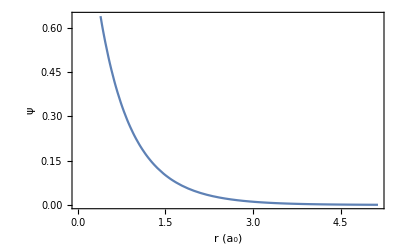

```mathematica
fig=Plot[ψguess[r]/(√c),{r,aplot,bplot},Frame->True,Axes->False,BaseStyle->(FontFamily->{"Times-Bold",14}),FrameLabel->{"r (a_0)","ψ"," "," "}];
(* Export["Fig/Radial.pdf",fig];*)
Show[fig]
```

### Define some functions of Hartree-Fock solutions for 1s orbital

```mathematica
(* radial function and differentiation *)
R[x_]=√(4π)ψguess[x]/(√c);
dR[x_]=√(4π)dψ[x]/(√c);
Jana[x_]=Jnum[x];

Js=NIntegrate[r^2 R[r]^2 Jana[r],{r,ai,bi}];
```

#### Extrapolate radial function outside [ai, bi]

```mathematica
Clear[r,coef];
coef=FindFit[Transpose[{rgrid,R[rgrid]}],√(4/c)√(zz^3)ⅇ^(-zz r),{zz},r];
R[x_/;x<ai||x>bi]=√(4/c)√(zz^3)ⅇ^(-zz x)/.coef;
```

### Inverse Laplace Transform

To compute the exchange potential, it is convenient to express the exact Hartree-Fock orbital as a Laplace transform of a function ω(t),

R(r) = ∫_0^∞ ⅇ^(-r t)ω(t)ⅆt

We have symbols for them,

ℒ[ω(t)] = R(r)
ℒ^-1[R(r)] = ω(t)

So, ω(t) is the inverse Laplace transform of R(r).

#### Week’s Method

Suppose ω(t) can be expressed as the limit of an expansion in scalar Laguerre polynomials,

ω(t) = ⅇ^(σ t)∑_(n=0)^∞ a_n ⅇ^(-β t)L_n(2 β t)

where β and σ are adjustable parameters, then the Laplace transform of ω(t) would get back the definition of R(r).

```mathematica
Clear[σ,β,i,rcoef,f,t,r];
f[t_]=ⅇ^((σ-β)t)LaguerreL[i,2β t];
rcoef=LaplaceTransform[f[t],t,r];
Print["r_coef: ",TraditionalForm[rcoef]];
Print[];
```

r_coef: ((-β)^i (2/(β+r-σ)-1/β)^i)/(β+r-σ)

So R(r) could be defined as,

R(r) = ∑_(n=0)^∞ a_n (r-β-σ)^n/(r+β-σ)^(n+1)

##### get coefficients

```mathematica
Clear[acoef,fit,Rdata,modelr,num,σ,β,r];

num=31;
σ=1;β=3;

Rdata=Transpose[{rgrid,R[rgrid]}];
modelr=∑_(i=0)^num acoef[i]rcoef;
fit=FindFit[Rdata,modelr,Table[acoef[i],{i,0,num}],r];
```

##### compare R(r) and fit function

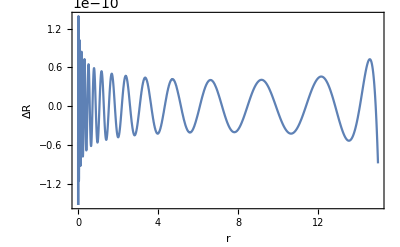

```mathematica
Clear[Rfit];
Rfit[r_]=modelr/.fit;

fig=Plot[R[r]-Rfit[r],{r,ai,bi},AxesLabel->{r,ΔR},WorkingPrecision->wpr,Frame->True,Axes->False];
(* Export["Fig/Rfit_comp.pdf",fig]; *)

Show[fig]
```

##### define ω(t)

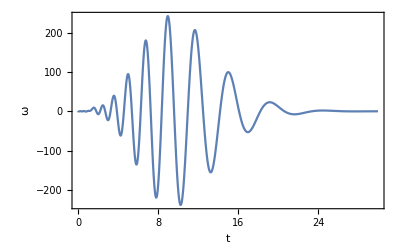

```mathematica
Clear[ω];
ω[t_]=∑_(i=0)^num acoef[i] ⅇ^((σ-β) t)LaguerreL[i,2β t]/.fit;

fig=Plot[ω[t],{t,0,30},PlotRange->All,AxesLabel->{t,ω},WorkingPrecision->wpr,Frame->True,Axes->False];
(* Export["Fig/wt.pdf",fig]; *)

Show[fig]
```

##### Laplace transform of ω(t) to check

```mathematica
Clear[Rback];
Rback[r_]=LaplaceTransform[ω[t],t,r];

fig=Plot[R[r]-Rback[r],{r,ai,bi},AxesLabel->{r,ΔR},WorkingPrecision->wpr,Frame->True,Axes->False];
(* Export["Fig/Rback_comp.pdf",fig]; *)

Show[fig]
```

-Graphics-

## Hylleraas solution for MP2 pair correlation function of He-like atom

### Get 3e integrals package

```mathematica
Get["int3e/Integrals_3e.m"];
```

### Some Parameters

#### Dimension of Equation

```mathematica
DE=1;
```

#### Exponential Factor

Variational parameter to make the MP2 energy lowest

```mathematica
solr=FindMinimum[-(r R[r])^2,{r,ai,bi}]⟦2⟧;
r=r/.solr;
ζ=Z/r;
```

#### Auxiliary Functions

```mathematica
Clear[σ,I1,I2,I3,I4,ϕ];
σ[l_?EvenQ]:=1;σ[l_]:=0;

ϕ[z_]:=R[z/ζ];

I1[a_,b_,c_]:=I1[a,b,c]=ζ^(a+b+c+6)/(c+2)NIntegrate[ⅇ^(-ζ (r1+r2)/2)R[r1]R[r2](r1^(a+1)r2^(b+1)+r1^(b+1)r2^(a+1))((r1+r2)^(c+2)-(r1-r2)^(c+2)),{r1,ai,bi},{r2,ai,r1},Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"}];

I2[a_,b_,c_]:=I2[a,b,c]=ζ^(a+b+c+8)/(c+2)NIntegrate[ⅇ^(-ζ(r1+r2)/2)R[r1]R[r2](Jana[r2] r1^(a+1)r2^(b+1)+Jana[r1] r1^(b+1)r2^(a+1))((r1+r2)^(c+2)-(r1-r2)^(c+2)),{r1,ai,bi},{r2,ai,r1},Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"}];

I3[a_,b_,c_]:=I3[a,b,c]=ζ^(a+b+c+8)/(c+2)NIntegrate[ⅇ^(-ζ(r1+r2))(Jana[r1] r1^(a+1)r2^(b+1)+Jana[r2] r1^(b+1)r2^(a+1))((r1+r2)^(c+2)-(r1-r2)^(c+2)),{r1,ai,bi},{r2,ai,r1}
,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"}];

I4[a_,b_,c_,m_,mp_]:=I4[a,b,c,m,mp]=ζ^(a+b+c+m+mp+8)/(16 π^3)NIntegrate[ω[t]ω[tp]I3e[a,b,c,m,mp,-1,t+ζ/2,tp+ζ/2,ζ],{t,0,30},{tp,0,30}
,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"}];
```

#### Prepare n, l, m

```mathematica
basis={};
index=0;
Do[If[-1≤n+l+m≤DE,
index++;
basis=Join[basis,{{n,l,m}}];
Print["i: ",index,"  n l m: ",n," ",l," ",m]]
,{n,0,DE},{l,0,DE,2},{m,0,DE}
];

dim=Length[basis];
Print["Dimension = ",dim];
Print[];
```

i: 1  n l m: 0 0 0

i: 2  n l m: 0 0 1

i: 3  n l m: 1 0 0

Dimension = 3

### Computation of Matrix M

#### T matrix

```mathematica
Clear[T]; 
T=Table[0,{i,dim},{j,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;{n2,l2,m2}=basis⟦j⟧;
p1=n1+l1+m1;
p2=n2+l2+m2;
q1=l1+m1;
q2=l2+m2;

T⟦i,j⟧=ζ^2/4(p1+p2+3)!*σ[l1+l2]*((4(p2+m2+1)(l2-n2+2)+(p1+p2)(4n2+4m2-p1-p2-1)+4)/(4(l1+l2+1)(q1+q2+3))-(m2(q2+l2+1))/((l1+l2+1)(q1+q2+1))-(l2(l2-1))/((l1+l2-1)(q1+q2+1))+(m2(m2+2n2-p1-p2-3))/((l1+l2+3)(q1+q2+3))+(4n2(n2-p1-p2-5)+(p1+p2+4)(p1+p2+5))/(4(l1+l2+3)(q1+q2+5)));
Print["T: ",i,"  ",j,": ",T⟦i,j⟧];
	
T⟦j,i⟧=T⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

T: 1  1: 24.6970093025228437018308754867284587784

T: 2  1: 77.17815407038388656822148589602643368251

T: 2  2: 395.1521488403654992292940077876553404545

T: 3  1: 98.78803721009137480732350194691383511362

T: 3  2: 416.7620319800729874683960238385427418856

T: 3  3: 543.3342046555025614402792607080260931249

#### V matrix

```mathematica
Clear[Vne]; 
Vne=Table[0,{i,dim},{j,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;{n2,l2,m2}=basis⟦j⟧;
p1=n1+l1+m1;
p2=n2+l2+m2;
q1=l1+m1;q2=l2+m2;

Vne⟦i,j⟧=-Z ζ σ[l1+l2] ((p1+p2+4)!)/((l1+l2+1)(q1+q2+3));
Print["V: ",i,"  ",j,": ",Vne⟦i,j⟧];
Vne⟦j,i⟧=Vne⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

V: 1  1: -56.22470267349507286173556680893340043991

V: 2  1: -210.8426350256065232315083755335002516496

V: 2  2: -1012.044648122911311511240202560801207918

V: 3  1: -281.1235133674753643086778340446670021995

V: 3  2: -1265.055810153639139389050253201001509898

V: 3  3: -1686.741080204852185852067004268002013197

#### J matrix (W)

```mathematica
Clear[W]; 
W=Table[0,{i,dim},{j,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;{n2,l2,m2}=basis⟦j⟧;

W⟦i,j⟧=2/ζ^2∑_(i1=0)^n1 ∑_(j1=0)^l1 ∑_(i2=0)^n2 ∑_(j2=0)^l2 ((-1)^(l1+l2-j1-j2)Binomial[n1,i1]Binomial[l1,j1]*Binomial[n2,i2]Binomial[l2,j2]*I3[i1+j1+i2+j2,n1+l1+n2+l2-i1-j1-i2-j2,m1+m2]);

Print["W: ",i,"  ",j,": ",W⟦i,j⟧];

W⟦j,i⟧=W⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

W: 1  1: 16.97350567498632306143596919360741435556

W: 2  1: 68.50823793301697139096533900906823988922

W: 2  2: 347.987711758899467456190481747908549112

W: 3  1: 93.60640705272492914198950072636569280672

W: 3  2: 442.6341308757056947546853317760747227581

W: 3  3: 604.1030518916815460281457429157621862474

#### K matrix

```mathematica
Clear[K]; 
K=Table[0,{i,dim},{j,dim}];
```

```mathematica
Clear[int];
Do[{n1,l1,m1}=basis⟦i⟧;{n2,l2,m2}=basis⟦j⟧;
K⟦i,j⟧=0;
Print["K: ",i,"  ",j,":"];
Do[Print["   ",n1+l1-i1-j1," ",n2+l2-i2-j2," ",i1+j1+i2+j2," ",m1," ",m2];
    int=I4[n1+l1-i1-j1,n2+l2-i2-j2,i1+j1+i2+j2,m1,m2];
    Print["     ",int];
    
    K⟦i,j⟧+=
	1/ζ^2(-1)^(l1+l2-j1-j2)Binomial[n1,i1]Binomial[l1,j1]*
	Binomial[n2,i2]Binomial[l2,j2]*int,
	{i1,0,n1},{j1,0,l1},{i2,0,n2},{j2,0,l2}];

Print[K⟦i,j⟧];
Print[];

K⟦j,i⟧=K⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

K: 1  1:

0 0 0 0 0

209.0161841706767730716176658694619492942

16.92643684993270790653767765584378115514

K: 2  1:

0 0 0 1 0

852.3423863844481466489717738599441520263

69.02393532300122237038345438814139402593

K: 2  2:

0 0 0 1 1

3945.645602660792367049590414646280998391

319.5241621630468112591815257882449554184

K: 3  1:

1 0 0 0 0

536.6010623616609269768009973939857635045

0 0 1 0 0

627.0485525120303192148529976083858478827

94.23405082127270814004388371947136136882

K: 3  2:

1 0 0 0 1

2535.560279428092092683823416614272974318

0 0 1 0 1

3042.297533905787097067658463167758936599

451.7030985419024829961510264290667936572

K: 3  3:

1 1 0 0 0

1460.5838567726845958380568500385240408

1 0 1 0 0

1609.803187084982780930402992181957290513

0 1 1 0 0

1609.803187084982780930402992181957290513

0 0 2 0 0

2508.194210048121276859411990433543391531

582.1259046338428595456883249298289712803

#### S matrix

```mathematica
Clear[S]; 
S=Table[0,{i,dim},{j,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;{n2,l2,m2}=basis⟦j⟧;
p1=n1+l1+m1;
p2=n2+l2+m2;
q1=l1+m1;q2=l2+m2;

S⟦i,j⟧=((q1+q2+l1+l2+6)(p1+p2+5)!)/(2(l1+l2+1)(l1+l2+3)(q1+q2+3)(q1+q2+5))*σ[l1+l2];
Print["S: ",i,"  ",j,": ",S⟦i,j⟧];

S⟦j,i⟧=S⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

S: 1  1: 8

S: 2  1: 35

S: 2  2: 192

S: 3  1: 48

S: 3  2: 245

S: 3  3: 336

#### S1 matrix

```mathematica
Clear[S1,sd]; 
S1=Table[0,{i,dim},{j,dim}];
sd=Table[0,{i,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;
sd⟦i⟧=1/(√2 ζ^3)∑_(i1=0)^n1 ∑_(j1=0)^l1 ((-1)^(l1-j1)Binomial[n1,i1]Binomial[l1,j1]*I1[i1+j1,n1+l1-i1-j1,m1]);
Print["sd: ",i,": ",sd⟦i⟧]
,
{i,dim}
];

Do[S1⟦i,j⟧=sd⟦i⟧*sd⟦j⟧;
S1⟦j,i⟧=S1⟦i,j⟧
,
{i,dim},{j,i}
];

Print[];
```

sd: 1: 2.810745537804086028941397361811602703396

sd: 2: 12.80917915365339993848142171472372007773

sd: 3: 17.50810295548635770595268448113813282986

#### M matrix

```mathematica
Clear[M];
M=Table[0,{i,dim},{j,dim}];

M=T+Vne+2W-K-2ϵ S+S1;
```

### Computation of Vector B

#### D vector

```mathematica
Clear[Dv]; 

Dv=Table[0,{i,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;
Dv⟦i⟧=ζ∑_(i1=0)^n1 ∑_(j1=0)^l1 ((-1)^(l1-j1)Binomial[n1,i1]Binomial[l1,j1]*I1[i1+j1,n1+l1-i1-j1,m1-1]);
Print["Dv: ",i,": ",Dv⟦i⟧]
,
{i,dim}
];

Print[];
```

Dv: 1: 183.6320666261835362107293170588702745394

Dv: 2: 606.1292845319883358516488745874656410249

Dv: 3: 942.8413472286183702101771360069139220241

#### X vector

```mathematica
Clear[Xv]; 

Xv=Table[0,{i,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;
Xv⟦i⟧=1/ζ^2∑_(i1=0)^n1 ∑_(j1=0)^l1 ((-1)^(l1-j1)Binomial[n1,i1]Binomial[l1,j1]*I2[i1+j1,n1+l1-i1-j1,m1]);
Print["Xv: ",i,": ",Xv⟦i⟧]
,
{i,dim}
];

Print[];
```

Xv: 1: 180.2267737880540223918578608957799257532

Xv: 2: 753.3299238668885462635615745317479569826

Xv: 3: 1025.572293415739962838328199292454808642

#### Y vector

```mathematica
Clear[Yv]; 

Yv=Table[0,{i,dim}];

Do[{n1,l1,m1}=basis⟦i⟧;
Yv⟦i⟧=Js∑_(i1=0)^n1 ∑_(j1=0)^l1 ((-1)^(l1-j1)Binomial[n1,i1]Binomial[l1,j1]*I1[i1+j1,n1+l1-i1-j1,m1]);
Print["Yv: ",i,": ",Yv⟦i⟧]
,
{i,dim}
];

Print[];
```

Yv: 1: 176.9324929171821009394352420889965458982

Yv: 2: 806.3198782659300737241531159270327973089

Yv: 3: 1102.110547006338019811206811991418382697

#### B vector

```mathematica
Clear[B];
B=Table[0,{i,dim}];

B=1/(2 ζ^3)(-Dv+2Xv-Yv);
```

### Solve M×C=B

```mathematica
Cv=LinearSolve[M,B ];
```

### Output M, C and B matrix

```mathematica
Print["M matrix: "];
Print["M = ",M//MatrixForm];
Print[];

Print["B vector: "];
Print["B = ",B//MatrixForm];
Print[];

Print["C vector: "];
Print["C = ",Cv//MatrixForm];
Print[];
```

M matrix:

M = (8.080461533840095344957981154744577891684 | 34.58829616525427086439428442698416837469 | 47.97784894326180411550513877339441130515
34.58829616525427086439428442698416837469 | 276.1287908982784741488480685892026549241 | 259.3340664320345060511745196466750612373
47.97784894326180411550513877339441130515 | 259.3340664320345060511745196466750612373 | 406.0731696125265720489132252040568443842)

B vector:

B = (-0.001279140497124665564712362640436300035082
1.085546949039114941340374640204277449634
0.07135558518728613593688918138664991615167)

C vector:

C = (-0.02063663295674492846436054590892714289352
0.01014809243759786686210572272905687366851
-0.003867010558676564385649223665921095608118)

### Calculate Pair Correlation Energy

```mathematica
E2=1/ζ^3∑_(i=1)^dim Cv⟦i⟧Dv⟦i⟧;

Print["E2 = ",E2];
Print[];
```

E2 = -0.02960070609678594595339401908675919101233

## Total MP2 Energy of He-Like Atom

```mathematica
Clear[Emp2];

Emp2=Ehf+E2;
```

## Results

### molpro MP2 computations (CCSD; two electrons have no triple excitations)

Sets                       E_hf.08              E_mp2                 E_2                    E_CCSD              E_2                   
        cc-pVDZ   -2.85516048   -2.88098882   -0.02582834         -2.88759483   -0.03243435       
        cc-pVTZ   -2.86115334   -2.89429091   -0.03313756         -2.90023217   -0.03907882      
        cc-pVQZ   -2.86151423   -2.89699223   -0.03547800        -2.90241088   -0.04089665       
 aug-cc-pVDZ   -2.85570467   -2.88266718   -0.02696251        -2.88954849   -0.03384382     
 aug-cc-pVTZ   -2.86118343   -2.89480424    -0.03362082        -2.90059792   -0.03941450      
 aug-cc-pVQZ  -2.86152200   -2.89724613    -0.03572413        -2.90253360   -0.04101160        
 aug-cc-pV5Z   -2.86162693   -2.89816115    -0.03653422        -2.90320053   -0.04157360
 aug-cc-pV6Z   -2.86167313   -2.89855506    -0.03688193        -2.90345535   -0.04178222

#### Focal point

```mathematica
Off[Solve::ifun];
Clear[ehf,e2];

ehf[4]=-2.861521995632`20;ehf[5]=-2.861626929246`20;ehf[6]=-2.861673128997`20;

e2[4]=-0.035724129513`20;e2[5]=-0.036534224848`20;e2[6]=-0.036881932607`20;

Clear[ah,bh,ch];
solh=Solve[Table[ah+bh ⅇ^(-ch x)==ehf[x],{x,4,6}],{ah,bh,ch}];
ehflimit=ah/.solh; 

Clear[ah,bh,ch];
solh=Solve[Table[ah+bh x^-3==e2[x],{x,5,6}],{ah,bh}];
e2limit=ah/.solh;

emp2=ehflimit+e2limit;

Print["Energy Focal Point (molpro) ---"];
Print["HF energy:   ",ehflimit⟦1⟧];
Print["correlation: ",e2limit⟦1⟧];
Print["Total MP2:   ",emp2⟦1⟧];
Print[];
```

Energy Focal Point (molpro) ---

HF energy:   -2.861709469480725070169486383008725307239

correlation: -0.03735955315507692307692307692307692307692

Total MP2:   -2.899069022635801993246409459931802230316

### Hylleraas MP2

#### debug: accudigit=6;ϵconv=10^-accudigit; wpr=10; agoal=6; pgoal=agoal;

#### real: accudigit=15;ϵconv=10^-accudigit; wpr=40; agoal=12; pgoal=agoal;

```mathematica
Print["Hylleraas energies: ---"];
Print["                 Z = ",Z];
Print["         HF Energy = ",Ehf];
Print["Correlation Energy = ",E2];
Print["      Total Energy = ",Emp2];
Print[];
```

Hylleraas energies: ---

Z = 2

HF Energy = -2.861679995595540874135334097307072641306

Correlation Energy = -0.02960070609678594595339401908675919101233

Total Energy = -2.891280701692326820088728116393831832318

### Comparisons

aug-cc-pV6Z:   E_hf= –2.861673128997   E_mp2 = –2.898555061604   E_2 = –0.036881932607
focal point:        E_hf= –2.861709469481   E_mp2= –2.899069022636   E_2= –0.037359553155

---------------------------------------------------------------------------------------------------------------------------------

debug 	debug (E_2)		real 			real (E_2)

---------------------------------------------------------------------------------------------------------------------------------

Hartree-Fock		–2.861621	     0		–2.861679995595540874             0

---------------------------------------------------------------------------------------------------------------------------------

DE=1, K=0		–2.887395	–0.025774	–2.887452781202837202	–0.025772785607296

DE=2, K=0		–2.893875        –0.032254        –2.893934247233085475        –0.032254251637545

DE=3, K=0		–2.894830	–0.033209	–2.894891438189288869         –0.033211442593785

DE = 4,  K = 0              –2.895079        –0.033458        –2.895151745292594563         –0.033471749697054

DE = 5,  K = 0              –2.895152        –0.033531        –2.895211109101802170         –0.033531113506261

DE = 6,  K = 0              –2.895169        –0.033548        –2.895228020770428293         –0.033548025174887

---------------------------------------------------------------------------------------------------------------------------------

DE=1, K ≠ 0		 –2.891226       –0.029604         –2.891280701692326974        –0.029600706096786

DE=2, K ≠ 0		                                                   –2.798199384927364774          0.063480610668176

DE=3, K ≠ 0	                                                               –2.920013638873829635         –0.058333643278289

DE=4, K ≠ 0

DE=5, K ≠ 0

DE=6, K ≠ 0

DE=7, K ≠ 0

DE=8, K ≠ 0

DE=9, K ≠ 0